## This notebook, calculates the frequency of a charged massles scalar field around a RN black hole considering a mirror: based on Phys Rev D 70 044039 (2004). Aveiro 20 feb 2013. check: mirrorFreq.mw

```mathematica
Exit
```

```mathematica
Clear; MaxExtraPrecision=100;
M=1;l=1; Q=0.999; r1 = 30; mu = 0.1;
```

```mathematica
winit=(0.2-0.00005*I)
```

0.2-0.00005 ⅈ

```mathematica
(*Define the Function of w as the solution of the Diferential equation given a value of r1, the position of the mirror. The returning value is the solution evaluated at r1 *)
```

```mathematica
LeavP1[w_?NumberQ]:=
Module[{Res},
qscal = 0.5; r0=rp+10^(-8); rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
```

```mathematica
(*Find the root of this function, this w is such as the value of the function is zero at *)
```

```mathematica
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

0.196017+2.16834×10^-7 ⅈ

```mathematica
(*Check that the solution obtained is the solution wanted and plot it*)
```

```mathematica
qscal = 0.5; r0=rp+10^(-8); rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ; wc=qscal*Q/rp
qsol=-Sqrt[mu*mu-wres*wres] ;
rhosol=-I*rp^2*(wres-wc)/(rp-rm);
sigmasol=(qscal*Q*wres+M*mu^2-2*M*wres^2);
(*potsol= 1/f*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2;*)
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  wres-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
```

0.478123

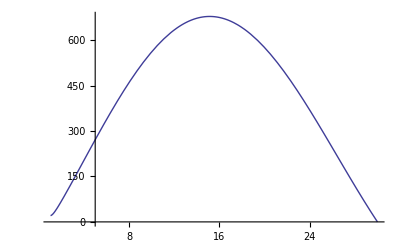

```mathematica
Plot[{2.01*Abs[Rs[r]/.sol]},{r,rp,r1}]
```

```mathematica
(*Now, do the previous procedure for several values of r1, the position of the mirror:
I approach the value from right and left because dont know the rate of change in the function,    in some cases is very high and then fails from one step to other.*)
```

```mathematica
winit=(0.20+0.000001*I);
ie=0;While[ie<201,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
qscal = 0.5 +ie/200; r0=rp+10^(-8); rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);

sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
qscals[ie]=qscal/mu;
winit=wres-0.001;
ie=ie+1
]
t1r=Table[{N[qscals[n],10],Re[witer[n]]},{n,0,200}];
t2r=Table[{N[qscals[n],10],Im[witer[n]]},{n,0,200}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

```mathematica
(*Calculate the values leftward*)
```

```mathematica
winit=(0.20+0.000001*I);
ie=0;While[ie<101,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
qscal = 0.5 - ie/200; r0=rp+10^(-8); rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);
(*potsol= 1/f*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2;*)
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
qscals[ie]=qscal/mu;
winit=wres+0.001;
ie=ie+1

]
t1l=Table[{N[qscals[n],10],Re[witer[n]]},{n,0,100}];t2l=Table[{N[qscals[n],10],Im[witer[n]]},{n,0,100}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

{{5.,2.16824×10^-7},{4.95,2.06724×10^-7},{4.9,1.96966×10^-7},{4.85,1.8754×10^-7},{4.8,1.78436×10^-7},{4.75,1.69657×10^-7},{4.7,1.61186×10^-7},{4.65,1.53021×10^-7},{4.6,1.45152×10^-7},{4.55,1.37575×10^-7},{4.5,1.30281×10^-7},{4.45,1.23265×10^-7},{4.4,1.16521×10^-7},{4.35,1.10041×10^-7},{4.3,1.03817×10^-7},{4.25,9.78461×10^-8},{4.2,9.21189×10^-8},{4.15,8.65966×10^-8},{4.1,8.13883×10^-8},{4.05,7.63519×10^-8},{4.,7.15457×10^-8},{3.95,6.69554×10^-8},{3.9,6.25744×10^-8},{3.85,5.83969×10^-8},{3.8,5.4418×10^-8},{3.75,5.06315×10^-8},{3.7,4.70334×10^-8},{3.65,4.36144×10^-8},{3.6,4.03732×10^-8},{3.55,3.73031×10^-8},{3.5,3.43987×10^-8},{3.45,3.16554×10^-8},{3.4,2.90672×10^-8},{3.35,2.66291×10^-8},{3.3,2.43372×10^-8},{3.25,2.21857×10^-8},{3.2,2.01696×10^-8},{3.15,1.8285×10^-8},{3.1,1.6526×10^-8},{3.05,1.48881×10^-8},{3.,1.33663×10^-8},{2.95,1.19578×10^-8},{2.9,1.06555×10^-8},{2.85,9.45603×10^-9},{2.8,8.35538×10^-9},{2.75,7.33047×10^-9},{2.7,6.42851×10^-9},{2.65,5.59455×10^-9},{2.6,4.84072×10^-9},{2.55,4.16254×10^-9},{2.5,3.55655×10^-9},{2.45,3.0154×10^-9},{2.4,2.53756×10^-9},{2.35,2.11724×10^-9},{2.3,1.75031×10^-9},{2.25,1.43196×10^-9},{2.2,1.15422×10^-9},{2.15,1.0834×10^-9},{2.1,7.20082×10^-10},{2.05,5.46799×10^-10},{2.,3.94221×10^-10},{1.95,2.57015×10^-10},{1.9,1.26261×10^-10},{1.85,-7.89757×10^-12},{1.8,-1.50064×10^-10},{1.75,-3.18604×10^-10},{1.7,-5.25725×10^-10},{1.65,-7.98074×10^-10},{1.6,-1.17182×10^-9},{1.55,-1.55083×10^-9},{1.5,-2.09995×10^-9},{1.45,-2.79647×10^-9},{1.4,-3.6983×10^-9},{1.35,-4.76096×10^-9},{1.3,-6.10284×10^-9},{1.25,-7.73913×10^-9},{1.2,-9.72139×10^-9},{1.15,-1.20944×10^-8},{1.1,-1.49093×10^-8},{1.05,-1.82593×10^-8},{1.,-2.21785×10^-8},{0.95,-2.67593×10^-8},{0.9,-3.20632×10^-8},{0.85,-3.81892×10^-8},{0.8,-4.52323×10^-8},{0.75,-5.32771×10^-8},{0.7,-6.24484×10^-8},{0.65,-7.28566×10^-8},{0.6,-8.46295×10^-8},{0.55,-9.78995×10^-8},{0.5,-1.12812×10^-7},{0.45,-1.29528×10^-7},{0.4,-1.48212×10^-7},{0.35,-1.69046×10^-7},{0.3,-1.92218×10^-7},{0.25,-2.17938×10^-7},{0.2,-2.46426×10^-7},{0.15,-2.77921×10^-7},{0.1,-3.1267×10^-7},{0.05,-3.5095×10^-7},{0.,-3.93039×10^-7}}

```mathematica
(*The imaginary part vs the radius*)
```

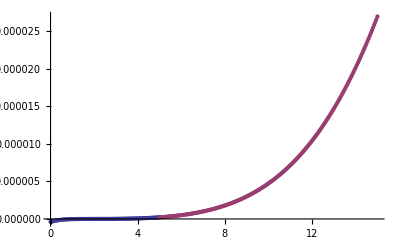

```mathematica
ListPlot[{t2l,t2r},Axes->True]
```

```mathematica
(*Real vs Radius*)
```

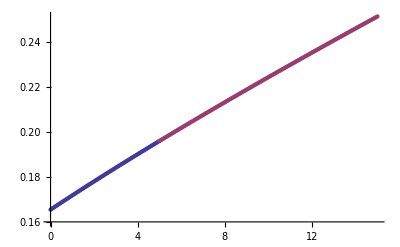

```mathematica
ListPlot[{t1l,t1r}]
```

```mathematica
Export["/home/h/skoli/pt/rnef/mathematica/q/mu0.1/r=30/Q=0.999/R.dat",Join[t1l,t1r]]
Export["/home/h/skoli/pt/rnef/mathematica/q/mu0.1/r=30/Q=0.999/I.dat",Join[t2l,t2r]]
```

/home/h/skoli/pt/rnef/mathematica/q/mu0.1/r=30/Q=0.999/R.dat

/home/h/skoli/pt/rnef/mathematica/q/mu0.1/r=30/Q=0.999/I.dat